# Lists Part 2

## Basic Exercises

### Question Subsection

Append the value 4 to {1, 2, 3}.

#### Solution

```mathematica
Append[{1,2,3},4]
```

{1,2,3,4}

### Question Subsection

Prepend the value 0 to {1, 2, 3}.

#### Solution

```mathematica
Prepend[{1,2,3},0]
```

### Question Subsection

Insert the value 3 into the correct position in the list {0, 1, 2, 4, 5}.

#### Solution

```mathematica
Insert[{0,1,2,4,5},3,4]
```

{0,1,2,3,4,5}

### Question Subsection

Delete the first element in Alphabet[].

#### Solution

```mathematica
alphabet = {a, b, c, d, e, f, g, h, i, j, k, l, m, n, o, p, q, r, s, t, u, v, w, x, y, z}
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Delete[alphabet,1]
```

{b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

### Question Subsection

Delete the vowels in Alphabet[].

#### Solution

```mathematica
Delete[alphabet,{{1},{5},{9},{15},{21}}]
```

{b,c,d,f,g,h,j,k,l,m,n,p,q,r,s,t,v,w,x,y,z}

### Question Subsection

Drop all characters after f in the alphabet.

#### Solution

```mathematica
Drop[alphabet,{7,-1}]
```

{a,b,c,d,e,f}

```mathematica
(* Or (i) Define the start position as the next index position after 'f'; (ii) the end position as the length of the vector; (iii) use the drop function accordingly*)
```

```mathematica
start=
FromDigits[
Flatten[
Position[alphabet,f]+1]]
```

```mathematica
end=Length[alphabet]
```

```mathematica
Drop[alphabet,{start,end}]
```

### Question Subsection

Generate a list of the hexadecimal digits i.e. {0, 1, 2, 3, 4, 5, 6, 7, 8, 9, a, b, c, d, e, f}

#### Solution

```mathematica
Join[Range[0,9],Drop[alphabet,{7,-1}]]
```

{0,1,2,3,4,5,6,7,8,9,a,b,c,d,e,f}

```mathematica
(* or *)
```

```mathematica
Join[Range[6],Drop[alphabet,{start,end}]]
```

{1,2,3,4,5,6,a,b,c,d,e,f}

### Question Subsection

Use PadRight to make a list of length 20 with the values {1, 2, 3, 1, 2, 3, ...}.

#### Solution

```mathematica
(* start with an empty list and pad it using the list {1, 2, 3} *)
```

```mathematica
PadRight[{},20,{1,2,3}]
```

{1,2,3,1,2,3,1,2,3,1,2,3,1,2,3,1,2,3,1,2}

## Advanced Exercise: Frequency Distribution of Roll of 3 Dice

The questions in this section are not independent. You must correctly answer each question in sequence!

### Question Subsection

If you roll 3 ordinary dice, the sum of each possible roll are:

```mathematica
sumOfRoles=Total/@Tuples[Range[6],3]
```

{3,4,5,6,7,8,4,5,6,7,8,9,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,4,5,6,7,8,9,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,6,7,8,9,10,11,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,11,12,13,14,15,16,7,8,9,10,11,12,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,11,12,13,14,15,16,12,13,14,15,16,17,8,9,10,11,12,13,9,10,11,12,13,14,10,11,12,13,14,15,11,12,13,14,15,16,12,13,14,15,16,17,13,14,15,16,17,18}

```mathematica
(* this is how it works *)
(* Generate a list corresponding to the faces of a single dice *)
Range[6]
```

{1,2,3,4,5,6}

```mathematica
(* generate all possible 3 combinations of the 3 dice *)
```

```mathematica
Tuples[Range[6],3]
```

{{1,1,1},{1,1,2},{1,1,3},{1,1,4},{1,1,5},{1,1,6},{1,2,1},{1,2,2},{1,2,3},{1,2,4},{1,2,5},{1,2,6},{1,3,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{1,3,6},{1,4,1},{1,4,2},{1,4,3},{1,4,4},{1,4,5},{1,4,6},{1,5,1},{1,5,2},{1,5,3},{1,5,4},{1,5,5},{1,5,6},{1,6,1},{1,6,2},{1,6,3},{1,6,4},{1,6,5},{1,6,6},{2,1,1},{2,1,2},{2,1,3},{2,1,4},{2,1,5},{2,1,6},{2,2,1},{2,2,2},{2,2,3},{2,2,4},{2,2,5},{2,2,6},{2,3,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5},{2,3,6},{2,4,1},{2,4,2},{2,4,3},{2,4,4},{2,4,5},{2,4,6},{2,5,1},{2,5,2},{2,5,3},{2,5,4},{2,5,5},{2,5,6},{2,6,1},{2,6,2},{2,6,3},{2,6,4},{2,6,5},{2,6,6},{3,1,1},{3,1,2},{3,1,3},{3,1,4},{3,1,5},{3,1,6},{3,2,1},{3,2,2},{3,2,3},{3,2,4},{3,2,5},{3,2,6},{3,3,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5},{3,3,6},{3,4,1},{3,4,2},{3,4,3},{3,4,4},{3,4,5},{3,4,6},{3,5,1},{3,5,2},{3,5,3},{3,5,4},{3,5,5},{3,5,6},{3,6,1},{3,6,2},{3,6,3},{3,6,4},{3,6,5},{3,6,6},{4,1,1},{4,1,2},{4,1,3},{4,1,4},{4,1,5},{4,1,6},{4,2,1},{4,2,2},{4,2,3},{4,2,4},{4,2,5},{4,2,6},{4,3,1},{4,3,2},{4,3,3},{4,3,4},{4,3,5},{4,3,6},{4,4,1},{4,4,2},{4,4,3},{4,4,4},{4,4,5},{4,4,6},{4,5,1},{4,5,2},{4,5,3},{4,5,4},{4,5,5},{4,5,6},{4,6,1},{4,6,2},{4,6,3},{4,6,4},{4,6,5},{4,6,6},{5,1,1},{5,1,2},{5,1,3},{5,1,4},{5,1,5},{5,1,6},{5,2,1},{5,2,2},{5,2,3},{5,2,4},{5,2,5},{5,2,6},{5,3,1},{5,3,2},{5,3,3},{5,3,4},{5,3,5},{5,3,6},{5,4,1},{5,4,2},{5,4,3},{5,4,4},{5,4,5},{5,4,6},{5,5,1},{5,5,2},{5,5,3},{5,5,4},{5,5,5},{5,5,6},{5,6,1},{5,6,2},{5,6,3},{5,6,4},{5,6,5},{5,6,6},{6,1,1},{6,1,2},{6,1,3},{6,1,4},{6,1,5},{6,1,6},{6,2,1},{6,2,2},{6,2,3},{6,2,4},{6,2,5},{6,2,6},{6,3,1},{6,3,2},{6,3,3},{6,3,4},{6,3,5},{6,3,6},{6,4,1},{6,4,2},{6,4,3},{6,4,4},{6,4,5},{6,4,6},{6,5,1},{6,5,2},{6,5,3},{6,5,4},{6,5,5},{6,5,6},{6,6,1},{6,6,2},{6,6,3},{6,6,4},{6,6,5},{6,6,6}}

```mathematica
(* Map the total function to each group of 3 numbers *)
```

Use Tally to obtain the distribution of the sumOfRoles. Set the result equal to sumFreq.

#### Solution

```mathematica
sumFreq=Tally[sumOfRoles]
```

{{3,1},{4,3},{5,6},{6,10},{7,15},{8,21},{9,25},{10,27},{11,27},{12,25},{13,21},{14,15},{15,10},{16,6},{17,3},{18,1}}

### Question Subsection

Use ListPlot to plot the frequency distribution of sumFreq.

#### Solution

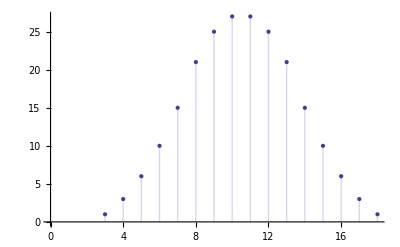

```mathematica
ListPlot[sumFreq,Filling->Axis]
```

## Advanced Exercise: Visualization of PDF of RandomInteger

The questions in this section are not independent. You must correctly answer each question in sequence!

### Question Subsection

The function RandomInteger generates random numbers:

```mathematica
?RandomInteger
```

RandomInteger[{i_min,i_max}] gives a pseudorandom integer in the range {i_min,i_max}. 
RandomInteger[i_max] gives a pseudorandom integer in the range {0,…,i_max}. 
RandomInteger[] pseudorandomly gives 0 or 1. 
RandomInteger[range,n] gives a list of n pseudorandom integers. 
RandomInteger[range,{n_1,n_2,…}] gives an n_1×n_2×… array of pseudorandom integers.

Use RandomInteger to generate a list of 100,000 random integers from 0 to 100. Set it equal to randInts.

#### Solution

```mathematica
randInts=Table[RandomInteger[100],{i,100000}];
```

```mathematica
(* or *)
```

```mathematica
RandomInteger[100,100000];
```

### Question Subsection

Find the frequency distribution of randInts and plot it with ListPlot. Does the distribution look uniform?

#### Hint

Use PlotRange → {Automatic, {0, Automatic}} in your ListPlot

#### Solution

```mathematica
?Tally
```

Tally[list] tallies the elements in list, listing all distinct elements together with their multiplicities.
Tally[list,test] uses test to determine whether pairs of elements should be considered equivalent, and gives a list of the first representatives of each equivalence class, together with their multiplicities.

```mathematica
(* the Tally funciton generates a frequency table for all values in the randInts list *)
```

```mathematica
ListPlot[Tally[randInts],Filling->Axis,PlotRange->{Automatic,{0,Automatic}}]
```

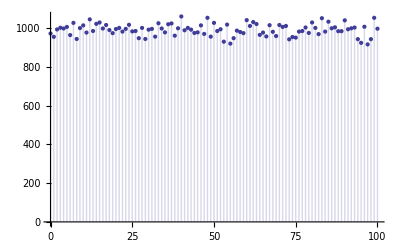

```mathematica
(* Qualitatively, the plot shows an almost uniform distribution of numbers *)
```

```mathematica
lst = Tally[randInts];
```

```mathematica
(* Standard deviation of each column *)
```

```mathematica
lst[[1]]
```

{70,1015}

```mathematica
StandardDeviation[lst]
```

{√(1717/2),(√(4750687/202))/5}

```mathematica
(* second column caries the frequency data - so measure the standard deviation of that *)
```

```mathematica
StandardDeviation[lst][[2]]//N
```

```mathematica
(* variance in frequency *)
```

30.6713

## Advanced Exercise: Make a Checkerboard

PadLeft and PadRight can do more than just pad with zeroes. It can also make cyclical patterns. For example:

```mathematica
PadRight[{a,b,c},10,{x,y}]
```

{a,b,c,y,x,y,x,y,x,y}

And it can even do it in more than 1 dimension:

```mathematica
PadRight[{{a,b},{c,d}},{6,6},{{1,2},{3,4}}]
```

{{a,b,1,2,1,2},{c,d,3,4,3,4},{1,2,1,2,1,2},{3,4,3,4,3,4},{1,2,1,2,1,2},{3,4,3,4,3,4}}

Use ArrayPlot and PadRight to make a checker board (chess board).

#### Solution

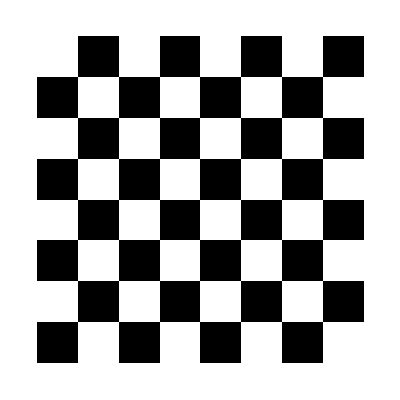

```mathematica
ArrayPlot[PadRight[{{}},{8,8},{{0,1},{1,0}}]]
```